# Analiza rodnosti in smrtnosti

## Analiza rodnosti in smrtnosti v Sloveniji med letoma 2000 in 2022

## Pridobivanje podatkov

Uvozila sem podatke, ki sem jih dobila na spletni strani stat.si in na strani eurostata.

```mathematica
podatki = Import["C:\\Users\\anate\\Downloads\\05I1002S_20240606-133326.csv","Table", FieldSeparators -> ";", HeaderLines -> 1 , CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"leto", "Živorojeni", "Umrli" } ]& //ResourceFunction["DatasetWithHeaders"]
```

Letnice sem spremenila v ustrezno obliko, da bojo leta na grafu prikazana pravilno.

```mathematica
podatki=Map[{DateObject[{#[[1]],1,1}],#[[2]],#[[3]]}&,podatki];
```

```mathematica
eupodatki = Import["C:\\Users\\anate\\Documents\\Ana\\ROM\\demo_gind__custom_11715059_page_spreadsheet.csv","Table", FieldSeparators -> ";", HeaderLines -> 2, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"država", "2002", "2003", "2004", "2005", "2006", "2007", "2008", "2009", "2010", "2011", "2012", "2013", "2014", "2015", "2016", "2017", "2018", "2019", "2020", "2021", "2022" } ]& //ResourceFunction["DatasetWithHeaders"]
```

## Analiza podatkov

Vidimo, da je v zadnjih letih število smrti strmo naraslo(v 2020 korona), število rojstev pa padlo.

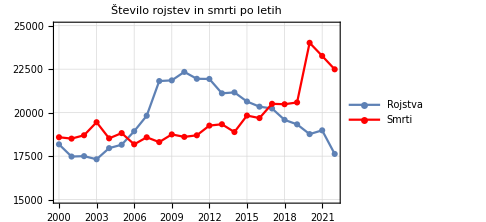

```mathematica
rojstva = DateListPlot[podatki[[All, {1,2}]],PlotRange->{15000,25000}, PlotTheme -> "FullAxesGrid", ImageSize -> Medium, PlotLegends -> LineLegend[{"Rojstva"}], PlotMarkers -> Automatic];
smrti =DateListPlot[podatki[All, {1,3}],PlotLabel->"Smrti po letih", PlotTheme -> "FullAxesGrid", ImageSize -> Medium, PlotLegends -> LineLegend[{"Smrti"}],PlotStyle->Red, PlotMarkers -> Automatic];
Show[rojstva, smrti, PlotLabel -> "Število rojstev in smrti po letih"]
```

Naravni prirastki po letih v Sloveniji med letoma 2002 in 2023.

```mathematica
slo =Query[Select[#država == "Slovenia"&] ]@eupodatki
```

```mathematica
sloPrirastek = Table[slo[[1]][[i]], {i, 2, 22}];
```

Graf prirastka po letih v Sloveniji

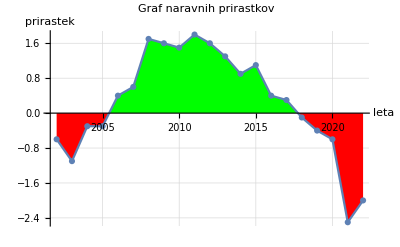

```mathematica
numerični=ToExpression[StringReplace[sloPrirastek,{","->".","b"->"1.6"}]];

ListLinePlot[numerični,DataRange -> {2002, 2022},Filling->Axis,FillingStyle->{Red,Green},PlotMarkers->Automatic,AxesLabel->{"leta","prirastek"},PlotLabel->"Graf naravnih prirastkov",GridLines->Automatic]
```

Prirastki v letu 2018, najbolj primerni pred obdobjem Covid-19.

```mathematica
podatki2018 =eupodatki[[;; 25]] //Query[All,{1,18}]
```

Primerjava Slovenije z drugimi državami v letu 2018. Vidimo, da je nekje v sredini.

```mathematica
euPrirastek = Table[podatki2018 [[i]][[2]], {i, 1, 25}];
```

```mathematica
euNumerični=ToExpression[StringReplace[euPrirastek,{","->".","b"->"1.6"}]];
```

```mathematica
države = Table[podatki2018 [[i]][[1]], {i, 1, 25}];
```

```mathematica
barve=If[#==="Slovenia",Blue, Pink]&/@države;
```

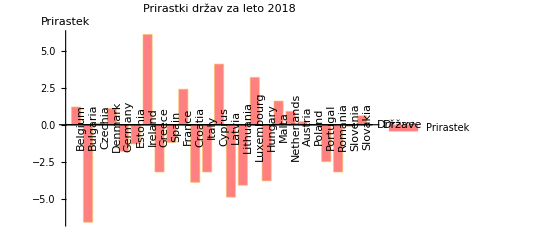

```mathematica
BarChart[euNumerični,ChartLabels-> Placed[države,Axis, Rotate[#, Pi / 2]&],ChartLegends->{"Prirastek"},PlotLabel->"Prirastki držav za leto 2018",AxesLabel->{"Države","Prirastek"}, ChartStyle->barve]
```